```mathematica
求根
```

```mathematica
r=52.4231;
FindRoot[{η^2+ξ^2==r,η==ξ Tan[ξ]},{ξ,1.3},{η,7}]
FindRoot[{η^2+ξ^2==r,η==ξ Tan[ξ]},{ξ,3.5},{η,6}]
FindRoot[{η^2+ξ^2==r,η==ξ Tan[ξ]},{ξ,6.5},{η,2.5}]
Clear[r]
```

{ξ→1.37915,η→7.10782}

{ξ→4.10892,η→5.96153}

{ξ→6.67941,η→2.79437}

```mathematica
计算第一个解的波函数
```

E = 0.0726 eV

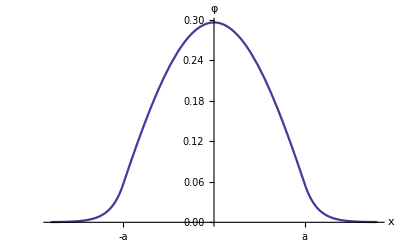

```mathematica
ξ=1.37914;a=10;V0=2;energy=3.81511×10^-2 ξ^2;Print["E = ",SetPrecision[energy,3]," eV"]
U[x_]:=If[Abs[x]≤a,0,V0];x0=1.8a;
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==10,
φ'[0]==0},φ,{x,-x0,x0}];
ma=NIntegrate[φ[x]^2/.First[s],
{x,-x0,x0}];
Plot[(φ[x]/.First[s])/√ma,{x,-x0,x0},
PlotRange->All,PlotStyle->Thickness[0.004],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},
AxesStyle->Thickness[0.003],
AxesLabel->{"x","φ"}]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```

```mathematica
第二个解
```

E = 0.644 eV

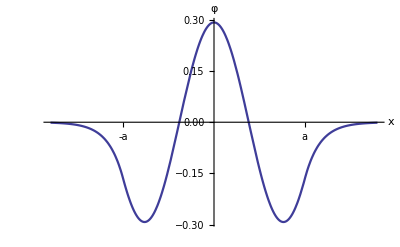

```mathematica
ξ=4.10892;a=10;V0=2;energy=3.81511*10^-2*ξ^2;Print["E = ",SetPrecision[energy,3]," eV"]
U[x_]:=If[Abs[x]≤a,0,V0];x0=1.8a;
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==10,
φ'[0]==0},φ,{x,-x0,x0}];
ma=NIntegrate[φ[x]^2/.First[s],
{x,-x0,x0}];
Plot[(φ[x]/.First[s])/√ma,{x,-x0,x0},
PlotRange->All,PlotStyle->Thickness[0.004],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},
AxesStyle->Thickness[0.003],AxesLabel->{"x","φ"}]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```

```mathematica
第三个解
```

E = 1.7 eV

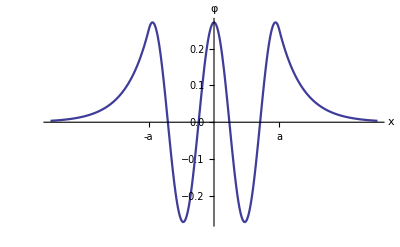

```mathematica
ξ=6.67941;a=10;V0=2;energy=3.81511*10^-2*ξ^2;Print["E = ",SetPrecision[energy,3]," eV"]
U[x_]:=If[Abs[x]≤a,0,V0];x0=2.5a;
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==10,
φ'[0]==0},φ,{x,-x0,x0}];
ma=NIntegrate[φ[x]^2/.First[s],
{x,-x0,x0}];
Plot[(φ[x]/.First[s])/√ma,{x,-x0,x0},
PlotRange->All,PlotStyle->Thickness[0.004],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},
AxesStyle->Thickness[0.003],AxesLabel->{"x","φ"}]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```

```mathematica
画能级图
```

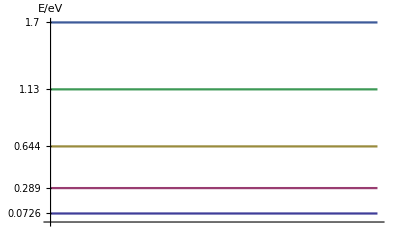

```mathematica
Plot[{0.0726,0.289,0.644,1.13,1.70},{x,0,1},
Ticks->{None,{0.0726,0.289,0.644,1.13,1.70}},
AxesLabel->{None,"E/eV"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```